## Possible Projects

- Night sky from other stars
- Floating polyhedron
- Black hole simulation
- Graphing smell
	http://www.ncbi.nlm.nih.gov/pmc/articles/PMC3782615/
	http://www.rachelherz.com/uploads/Emotion_experienced_during_encoding_AJP_1997.pdf
	http://digitalcommons.csbsju.edu/cgi/viewcontent.cgi?article=1007&context=psychology_students
- Cymatics
	http://delivery.acm.org/10.1145/2610000/2601119/a79-davis.pdf?ip=141.133.110.247&id=2601119&acc=OA&key=E617A8D0AC08EE50%2E4D4702B0C3E38B35%2E4D4702B0C3E38B35%2ECECA88AB440B5DAB&CFID=691028941&CFTOKEN=92897014&__acm__=1436288475_44eba09787d2b46e2d6a1b8eca66974d
	http://alice.loria.fr/publications/papers/2006/SMI_Laplacian/SMI_Laplacian.pdf
	http://www.sciencebuddies.org/science-fair-projects/phpBB3/viewtopic.php?f=30&t=6660

## Cymatics

### Research

#### Eigenvalues and eigenvectors:

Imagine a vector being tranformed under the rule T. There are vectors for which the transformed product is a scaled version of the original (lambda * vector), which means it could be stretched, flipped, or remain the same. These vectors are called Eigenvectors, and the scale (lambda) is the Eigenvalue for tranformation T.

```mathematica
The number at the end denotes the number of eigenvalues and functions, (the nth harmonic?). The heigenvalue is the fundamental frequency?
```

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Disk[],10];
```

```mathematica
Table[Plot3D[funs⟦i⟧,{x,y}∈Disk[],PlotRange->All,PlotLabel->vals⟦i⟧,PlotTheme->"Minimal"],{i,Length[vals]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
NDEigensystem[2, 3, 4, 5]
```

NDEigensystem[2,3,4,5]

```mathematica
what is differential 

ND solve
```

differential is what

ND solve

```mathematica
? NDEigensystem
```

RowBox[{"NDEigensystem", "[", RowBox[{RowBox[{StyleBox["ℒ", "TI"], "[", RowBox[{StyleBox["u", "TI"], "[", StyleBox[RowBox[{"x", ",", "y", ",", "…"}], "TI"], "]"}], "]"}], ",", StyleBox["u", "TI"], ",", RowBox[{StyleBox[RowBox[{"{", RowBox[{"x", ",", "y", ",", "…"}], "}"}], "TI"], "∈", StyleBox["Ω", "TR"]}], ",", StyleBox["n", "TI"]}], "]"}] gives the StyleBox["n", "TI"] smallest magnitude eigenvalues and eigenfunctions for the linear differential operator StyleBox["ℒ", "TI"] over the region StyleBox["Ω", "TR"].
RowBox[{RowBox[{"NDEigensystem", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["ℒ", "TI"], StyleBox["1", "TR"]], "[", RowBox[{RowBox[{StyleBox["u", "TI"], "[", StyleBox[RowBox[{"x", ",", "y", ",", "…"}], "TI"], "]"}], ",", RowBox[{StyleBox["v", "TI"], "[", StyleBox[RowBox[{"x", ",", "y", ",", "…"}], "TI"], "]"}], ",", StyleBox["…", "TR"]}], "]"}], ",", RowBox[{SubscriptBox[StyleBox["ℒ", "TI"], StyleBox["2", "TR"]], "[", RowBox[{RowBox[{StyleBox["u", "TI"], "[", StyleBox[RowBox[{"x", ",", "y", ",", "…"}], "TI"], "]"}], ",", RowBox[{StyleBox["v", "TI"], "[", StyleBox[RowBox[{"x", ",", "y", ",", "…"}], "TI"], "]"}], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{StyleBox[RowBox[{"{", RowBox[{"x", ",", "y", ",", "…"}], "}"}], "TI"], "∈", StyleBox["Ω", "TR"]}], ",", StyleBox["n", "TI"]}], "]"}], " "}] gives eigenvalues and eigenfunctions for the coupled differential operators RowBox[{"{", RowBox[{SubscriptBox[StyleBox["op", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["op", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}] over the region StyleBox["Ω", "TR"].
RowBox[{"NDEigensystem", "[", RowBox[{StyleBox["eqns", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["t", "TI"], ",", RowBox[{StyleBox[RowBox[{"{", RowBox[{"x", ",", "y", ",", "…"}], "}"}], "TI"], "∈", StyleBox["Ω", "TR"]}], ",", StyleBox["n", "TI"]}], "]"}] gives the eigenvalues and eigenfunctions in the spatial variables StyleBox[RowBox[{"{", RowBox[{"x", ",", "y", ",", "…"}], "}"}], "TI"] for solutions RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}] of the coupled time-dependent differential equations StyleBox["eqns", "TI"].

# Test

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Disk[],20];
```

```mathematica
vals
```

{5.78323,14.6827,14.6828,26.3785,26.3794,30.4791,40.7221,40.7227,49.249,49.252,57.6259,57.6279,70.9282,70.9454,74.9877,77.0416,77.0462,95.4913,95.4972,98.9246}

```mathematica
Clear[vals]
```

```mathematica
(*Manipulate[Plot3D[funs⟦i⟧,{x,y}∈Disk[],PlotRange->All,PlotLabel->vals⟦i⟧,PlotTheme->"Minimal"],{i,1,Length[vals], 1}];*)
```

```mathematica
Ω=Disk[];
{vals, funs} = NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u,{x,y}∈Ω,6];
```

```mathematica
ranges = Map[Max[Abs[Last[PlotRange /. Options[Plot3D[#[x,y],{x,y}∈Ω]]]]]&,funs];
row[t_] := Grid[{MapThread[Plot3D[Sin[Sqrt[#1] t] #2[x,y] ,{x,y}∈Ω,PlotRange->#3{-1,1},Axes->False,Mesh->False]&,{vals,funs,ranges}]}]
```

```mathematica
rows = Table[row[t],{t,0,2 Pi/Sqrt[vals[[1]]],.1}];
```

```mathematica
ListAnimate[rows]
```

ListAnimate[rows]

```mathematica
PlotRange /. Options[Plot3D[#[x,y],{x,y}∈Ω]]
```

{{-1.,1.},{-0.997204,0.997204},{0.,0.}}

```mathematica
vals
```

{5.78323,14.6827,14.6828,26.3785,26.3794,30.4791}

```mathematica
lct[t_,x_,y_]:=4(Cos[Sqrt[vals] t]/vals).Map[#[x,y]&,funs]
```

```mathematica
plots = Table[Plot3D[lct[t,x,y],{x,y}∈Ω,PlotRange->{-1.2,1.2},Mesh->False],{t,0,10,.25}];
ListAnimate[plots]
```

```mathematica
w = NDSolveValue[{D[u[t,x,y],t,t]== Laplacian[u[t,x,y],{x,y}],DirichletCondition[u[t,x,y]==0,True],u[0,x,y]==lct[0,x,y],(D[u[t,x,y],t] /.t->0)== (D[lct[t,x,y],t] /. t->0)},u,{t,0,10},{x,y}∈Ω];
```

```mathematica
Block[{t = 10},Plot3D[w[t,x,y] - lct[t,x,y],{x,y}∈Ω]]
```

# Code

## Perfect Elastic Bounce

### Graphics of a Disk and Boundaries

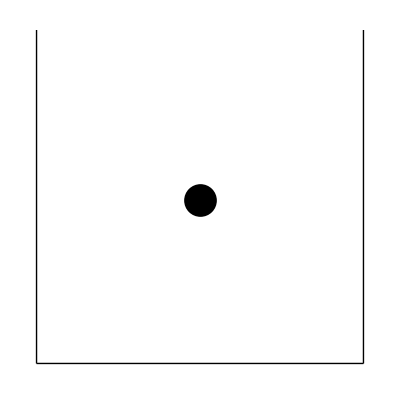

```mathematica
Graphics[{Disk[{.5,.5},.05],Line[{{0,1000},{0,0},{1,0},{1,1000}}]},PlotRange->{0,1}]
```

```mathematica
With[{t=0},
Graphics[{Disk[{.5,Sin[t]+.5},.05],Line[{{0,1000},{0,0},{1,0},{1,1000}}]},PlotRange->{0,1}]
]
```

-Graphics-

```mathematica
Manipulate[Graphics[{Disk[{.5,Sin[t]+1.5},.05],Line[{{0,1000},{0,0},{1,0},{1,1000}}]},PlotRange->{0,5}],
{t,0,10}
]
```

```mathematica
Animate[Graphics[{Disk[{.5,Sin[t]+1.5},.05],Line[{{0,1000},{0,0},{1,0},{1,1000}}]},PlotRange->{0,5}],
{t,0,10}
]
```

### Find the Function Through Solving Differential Equation

#### Solution is an equation that models the movement of the disk. Find the first function that can solve the differential equation where y’’[t] is the acceleration, y’[t] is the velocity, and y[t] is the position. Since f = ma, if mass is assumed to be 1, the acceleration would just be the force of gravity -9.8. Solve the equation for when t goes from 0 to 100.

```mathematica
solns=First@NDSolve[{y''[t]==-9.8,y[0]==10,y'[0]==0},y,{t,0,100}]
```

{y→InterpolatingFunction[{{0., 100.}}, <>]}

```mathematica
Replace y[t] with the function in solns first with evaluate, then plot the results for when t -> 100.
```

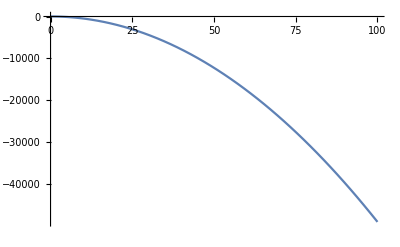

```mathematica
Plot[Evaluate[y[t]/.solns],{t,0,100}]
```

#### However, since we want the ball to reverse directions when near floor, use WhenEvent to monitor the NDSolve value and control the actions of the bounce when 0.05 near floor.

```mathematica
solns=First@NDSolve[{y''[t]==-9.8,y[0]==10,y'[0]==0,WhenEvent[y[t]-0≤0.05, y'[t]-> -y'[t]]},y,{t,0,10}]
```

{y→InterpolatingFunction[{{0., 10.}}, <>]}

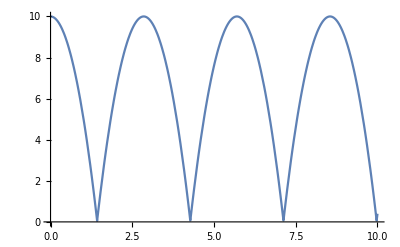

```mathematica
Plot[Evaluate[y[t]/.solns],{t,0,10}]
```

```mathematica
Animate[Graphics[{Disk[{.5,Evaluate[y[t]/.solns]},.05],Line[{{0,1000},{0,0},{1,0},{1,1000}}]},PlotRange->{0, 15}],
{t,0,5}

]
```

```mathematica
solns=First@NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]-0≤0.05, y'[t]-> -y'[t]]},y,{t,0,10}]
```

{y→InterpolatingFunction[{{0., 10.}}, <>]}

```mathematica
Animate[Graphics[{Disk[{2.5,Evaluate[y[t]/.solns]},.2],Line[{{0,1000},{0,0},{5,0},{5,1000}}]},PlotRange->{0, 6}],
{t,0,5}
]
```

## Inelastic Bounce

```mathematica
solns=First@NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]-0≤0.05, y'[t]-> -y'[t]]},y,{t,0,10}]
```

{y→InterpolatingFunction[{{0., 10.}}, <>]}

```mathematica
Animate[Graphics[{Disk[{2.5,Evaluate[y[t]/.solns]},.2],Line[{{0,1000},{0,0},{5,0},{5,1000}}]},PlotRange->{0, 6}],
{t,0,5}
]
```

### Add Diminishing Ratio to the Velocity

#### When the ball bounces off the floor, instead of only reversing the direction of the velocity, make it only a portion of the original as well.

```mathematica
solns=First@NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]-0≤0.05, y'[t]-> -0.8y'[t]]},y,{t,0,10}]
```

{y→InterpolatingFunction[{{0., 10.}}, <>]}

```mathematica
Animate[Graphics[{Disk[{2.5,Evaluate[y[t]/.solns]},.2],Line[{{0,1000},{0,0},{5,0},{5,1000}}]},PlotRange->{0, 6}],
{t,0,5}
]
```

## Now Move the Floor

```mathematica
solns=First@NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]-Sin[t]≤0.05, y'[t]-> -0.8y'[t]]},y,{t,0,10}]
```

{y→InterpolatingFunction[{{0., 10.}}, <>]}

```mathematica
Module[{floor},

floor[t_]:=Sin[t];

Animate[Graphics[{Disk[{2.5,Evaluate[y[t]/.solns]},.2],Line[{{0,1000},{0,floor[t]},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,0,5}
]

]
```

#### Want to put both the solns and the animate in a module so that there can be non global variables.

```mathematica
Module[{floor,solns,tmin=0,tmax=25},

floor[t_]:=Sin[t];

solns=First@NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]-floor[t]<= 0.05, y'[t]-> -0.8y'[t]]},y,{t,tmin,tmax}];

Animate[Graphics[{Disk[{2.5,Evaluate[y[t]/.solns]},.05],Line[{{0,1000},{0,floor[t]},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax},AnimationRate->.8
]

]
```

#### Sometimes the ball falls through the floor because it doesn’t know how to stop, so we should set another condition that once the ball’s velocity is close enough to the floor’s, set its position to the position of the floor.

```mathematica
Module[{floor,solns,tmin=0,tmax=25},

floor[t_]:=Sin[t];

solns=First@NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]-floor[t]<= 0.25,y'[t]-> -0.8y'[t]]},y,{t,tmin,tmax}];

Animate[Graphics[{Disk[{2.5,Evaluate[y[t]/.solns]},.2],Line[{{0,1000},{0,floor[t]},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax},AnimationRate->.8
]
]
```

#### For now, let’s move on and add another ball.

```mathematica
Module[{floor,solns,solns2,tmin=0,tmax=25},

floor[t_]:=Sin[t];

solns=First@NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]-floor[t]<= 0.25,y'[t]-> -0.8y'[t]]},y,{t,tmin,tmax}];

solns2=First@NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]-floor[t]<= 0.25,y'[t]-> -0.8y'[t]]},y,{t,tmin,tmax}];

Animate[Graphics[{Disk[{3.5,Evaluate[y[t]/.solns]},.2],Disk[{1.5,Evaluate[y[t]/.solns2]},.2],Line[{{0,1000},{0,floor[t]},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax},AnimationRate->.8
]
]
```

#### Now let’s tilt the floor so the balls can bounce at angles. BUG FIXED**

```mathematica
Module[{floor,floorV, slope, solns,solns2,tmin=0,tmax=25, diskR = 0.2, ratio = 0.8},

floor[t_] := Sin[t];
floorV[t_]:= Cos[t];
slope[t_, x_]:=floor[t]*x/5;

solns=First@NDSolve[{y''[t]==-9.81,y[0]==5,y'[0]==0,WhenEvent[y[t]-slope[t, 3.5]≤ diskR,y'[t]-> 2floorV[t]-ratio y'[t]]},y,{t,tmin,tmax}];

solns2=First@NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]-slope[t, 1.5]≤ diskR,y'[t]-> 2 floorV[t]-ratio y'[t]]},y,{t,tmin,tmax}];

Animate[
Graphics[
{Disk[
{3.5,Evaluate[If[y[t]-slope[t, 3.5]< diskR, slope[t, 3.5] + diskR, y[t]]/.solns]},diskR],
Disk[
{1.5,Evaluate[If[y[t]- slope[t, 1.5] < diskR, slope[t, 1.5]+ diskR, y[t]]/.solns2]},diskR],Line[{{0,1000},{0,0},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax},AnimationRate->.8
]
]
```

## Add in Another Dimension

### Finding the Vector of Bounce

#### Write a function for which if you detect a contact between the ball and the floor (based on y[t]), input the current velocity of the ball (x’[t]), angle at which it hits the floor, and output the new velocity

#### The momentum is conserved: velocity of ball x initial + velocity of floor x initial = -velocity of ball x final - velocity of floor final). Since the velocity of the floor does not change based on the collision, its simplified to vxf = -(vxi + 2vf). Vector angle between x’[t] and slope[t, x]. The bounce velocity is slope - that angle.

```mathematica
Quiet@Module[{floor,floorV, slope, solns,solns2,tmin=0,tmax=25, diskR = 0.2, ratio = 0.8, vx},

floor[t_] := Sin[t];
floorV[t_]:= Cos[t];
slope[t_, x_]:=floor[t]*x/5;
vx[xt_,t_,x_] :=  xt Cos[2 (slope[t,x] + VectorAngle[xt, slope[t,x]])];

solns=First@NDSolve[{x''[t]== 0, x[0]== 3.5,x'[0] == 1,
y''[t]==-9.81,y[0]==5,y'[0]==0,
WhenEvent[(x[t]≤ diskR|| x[t]≥ 5-diskR),
x'[t]-> -x'[t] ],
WhenEvent[y[t]-slope[t, x[t]]≤ diskR,
{y'[t]-> 2floorV[t]-ratio y'[t],
x'[t]-> vx[x'[t], t, x[t]]}]},
{x,y},{t,tmin,tmax}];

solns2=First@NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]-slope[t, 1.5]≤ diskR,y'[t]-> 2 floorV[t]-ratio y'[t]]},y,{t,tmin,tmax}];

Animate[
Graphics[
{Disk[
{x[t]/. solns,Evaluate[If[y[t]-slope[t, x[t]]< diskR, slope[t, x[t]] + diskR, y[t]]/.solns]},diskR],
Disk[
{1.5,Evaluate[If[y[t]- slope[t, 1.5] < diskR, slope[t, 1.5]+ diskR, y[t]]/.solns2]},diskR],Line[{{0,1000},{0,0},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax},AnimationRate->.8
]
]
```

```mathematica
Module[{floor,floorV, floorEq, solns,solns2,tmin=0,tmax=25, diskR = 0.05, ratio = 0.8, vx, xcoor, vy, v},

floor[t_] := Sin[t];
floorV[t_]:= Cos[t];
floorEq[t_, x_]:=floor[t]*x/5;
v[xt_, yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_, y_] :=  v[xt,yt] Cos[2 (VectorAngle[AngleVector[xt], AngleVector[90-(floor[t]/5)]])+ ArcTan[xt/yt]];

xcoor = RandomReal[{0.05, 4.95}];

solns=First@NDSolve[{x''[t]== 0, x[0]== xcoor,x'[0] == 0,
y''[t]==-9.81,y[0]==2,y'[0]==0,
WhenEvent[(x[t]≤ diskR|| x[t]≥ (5-diskR)),
x'[t]->-x'[t]],
WhenEvent[y[t]-floorEq[t, x[t]]≤ diskR,
{y'[t]-> 2floorV[t]-ratio y'[t],
x'[t]-> vx[x'[t],y'[t], t, x[t], y[t]]}]},
{x,y},{t,tmin,tmax}];

Animate[
Graphics[
{Disk[
{x[t]/. solns,Evaluate[If[y[t]-floorEq[t, x[t]]< diskR, floorEq[t, x[t]] + diskR, y[t]]/.solns]},diskR],
Line[{{0,1000},{0,0},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax},AnimationRate->.8
]
]
```

```mathematica
Module[{floor,floorV, floorEq, solns,solns2,tmin=0,tmax=25, diskR = 0.05, ratio = 0.8, vx, xcoor, vy, v},

floor[t_] := Sin[t];
floorV[t_]:= Cos[t];
floorEq[t_, x_]:=floor[t]*x/5;
v[xt_, yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_, y_] :=  v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]], AngleVector[90-(floor[t]/5)]]))];

xcoor = RandomReal[{0.05, 4.95}];

solns=First@NDSolve[{x''[t]== 0, x[0]== xcoor,x'[0] == 0,
y''[t]==-9.81,y[0]==5,y'[0]==0,
WhenEvent[y[t]-floorEq[t, x[t]]≤ diskR,
{y'[t]-> 2floorV[t]-ratio y'[t],x'[t]->vx[x'[t], y'[t], t, x[t], y[t]]}],
WhenEvent[(x[t]≤ diskR|| x[t]≥ (5-diskR)),
x'[t]->- ratio x'[t]]},
{x,y},{t,tmin,tmax}];

Animate[
Graphics[
{Disk[
{x[t]/. solns,Evaluate[If[y[t]-floorEq[t, x[t]]< diskR, floorEq[t, x[t]] + diskR, y[t]]/.solns]},diskR],
Line[{{0,1000},{0,0},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax}, AnimationRate->.5
]
]
```

## Automatically Generate Particles

```mathematica
Module[{floor,floorV, floorEq, solns,solns2,tmin=0,tmax=25, diskR = 0.05, ratio = 0.8, vx, xcoor, vy, v, listsolns},

floor[t_] := Sin[t];
floorV[t_]:= Cos[t];
floorEq[t_, x_]:=floor[t]*x/5;
v[xt_, yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_, y_] :=  v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]], AngleVector[90-(floor[t]/5)]]))];

listsolns:=List[];
For[i=0, i< 10, i++, {xcoor = RandomReal[{0.05, 4.95}],AppendTo[listsolns, solns]}];

solns=First@NDSolve[{x''[t]== 0, x[0]== xcoor,x'[0] == 0,
y''[t]==-9.81,y[0]==5,y'[0]==0,
WhenEvent[y[t]-floorEq[t, x[t]]≤ diskR,
{y'[t]-> 2floorV[t]-ratio y'[t],x'[t]->vx[x'[t], y'[t], t, x[t], y[t]]}],
WhenEvent[(x[t]≤ diskR|| x[t]≥ (5-diskR)),
x'[t]->- ratio x'[t]]},
{x,y},{t,tmin,tmax}];

Animate[
Graphics[
{Table[Disk[
{x[t],Evaluate[If[y[t]-floorEq[t, x[t]]< diskR, floorEq[t, x[t]] + diskR, y[t]]/.listsolns[[i]]]},diskR], {i, 0, 10}],
Line[{{0,1000},{0,0},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax}, AnimationRate->.5
]
]
```

#### The for loop now works so that if you ask for listsolns[[i]] it can return the list of functions.

```mathematica
Quiet@ Module[{floor,floorV, floorEq, solns,solns2,tmin=0,tmax=25, diskR = 0.05, ratio = 0.8, vx, xcoor, vy, v, listsolns},

floor[t_] := Sin[t];
floorV[t_]:= Cos[t];
floorEq[t_, x_]:=floor[t]*x/5;
v[xt_, yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_, y_] :=  v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]], AngleVector[90-(floor[t]/5)]]))];

listsolns=List[];
For[i=1, i< 10, i++, {xcoor = RandomReal[{0.05, 4.95}],solns=First@NDSolve[{x''[t]== 0, x[0]== xcoor,x'[0] == 0,
y''[t]==-9.81,y[0]==5,y'[0]==0,
WhenEvent[y[t]-floorEq[t, x[t]]≤ diskR,
{y'[t]-> 2floorV[t]-ratio y'[t],x'[t]->vx[x'[t], y'[t], t, x[t], y[t]]}],
WhenEvent[(x[t]≤ diskR|| x[t]≥ (5-diskR)),
x'[t]->- ratio x'[t]]},
{x,y},{t,tmin,tmax}],
AppendTo[listsolns, solns]}];

Animate[
Graphics[
{Table[Disk[
{x[t]/.listsolns[[i]],Evaluate[ If[y[t]-floorEq[t, x[t]]< diskR, floorEq[t, x[t]] + diskR,y[t]]/.listsolns[[i]]]},diskR], {i,1,10}],
Line[{{0,1000},
{0,0},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax}, AnimationRate->1
]
]
```

#### One ball kinda works with the new system..

```mathematica
Module[{floor,floorV, floorEq, solns,solns2,tmin=0,tmax=25, diskR = 0.05, ratio = 0.8, vx, xcoor, vy, v},

floor[t_] := Sin[t];
floorV[t_]:= Cos[t];
floorEq[t_, x_]:=floor[t]*x/5;
v[xt_, yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_, y_] :=  v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]], AngleVector[90-(floor[t]/5)]]))];

xcoor = RandomReal[{0.05, 4.95}];

solns=First@NDSolve[{x''[t]== 0, x[0]== xcoor,x'[0] == 0,
y''[t]==-9.81,y[0]==5,y'[0]==0,
WhenEvent[y[t]-floorEq[t, x[t]]≤ diskR,
{y'[t]-> 2floorV[t]-ratio y'[t],x'[t]->vx[x'[t], y'[t], t, x[t], y[t]]}],
WhenEvent[(x[t]≤ diskR|| x[t]≥ (5-diskR)),
x'[t]->- ratio x'[t]]},
{x,y},{t,tmin,tmax}];

Animate[
Graphics[
{Disk[
{x[t]/. solns,Evaluate[If[y[t]-floorEq[t, x[t]]< diskR, floorEq[t, x[t]] + diskR, y[t]]/.solns]},diskR],
Line[{{0,1000},{0,0},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax}, AnimationRate->.5
]
]
```

```mathematica
Module[{floor,floorV, floorEq, solns,solns2,tmin=0,tmax=25, diskR = 0.05, ratio = 0.8, vx, xcoor, vy, v, numDisks = 10},

floor[t_] := Sin[t];
floorV[t_]:= Cos[t];
floorEq[t_, x_]:=floor[t]*x/5;
v[xt_, yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_, y_] :=  v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]], AngleVector[90-(floor[t]/5)]]))];

xcoor = RandomReal[{0.05, 4.95}];

solns=NDSolve[Table[{y[i]''[t]==-9.81,y[i][0]==5,y[i]'[0]==0,
WhenEvent[y[#][t]-Sin[t]≤ diskR,
y[#]'[t]-> 2floorV[t]-ratio y[#]'[t]] &[i]},{i , 1, numDisks}],
Table[y[i], {i, 1, numDisks}],{t,tmin,tmax}];

Animate[
Graphics[
{Table[Disk[
Flatten[{3,Evaluate[If[y[#][t]-Sin[t]< diskR, Sin[t] + diskR, y[#][t]]&[i]/.solns]}],diskR],{i, 1, numDisks}],
Line[{{0,1000},{0,0},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax}, AnimationRate->.5
]
]
```

#### The balls now are generated but they fall uniformly in a line.

```mathematica
Module[{floor,floorV,floorEq,solns,tmin=0,tmax=25,diskR = 0.05,ratio = 0.8,vx,xcoor,vy,v,numDisks = 10},

floor[t_] := Sin[t];
floorV[t_]:= Cos[t];
floorEq[t_,x_]:=floor[t]*x/5;
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floor[t]/5)]]))];
xcoor = RandomReal[{0.05,4.95}];

solns=First@NDSolve[Table[{x[i]''[t]== 0,x[i][0]== RandomReal[{0.05,4.95}],x[i]'[0] == 0,
y[i]''[t]==-9.81,y[i][0]==5,y[i]'[0]==0,
WhenEvent[y[#][t]-Sin[t]≤ diskR,
y[#]'[t]-> 2floorV[t]-ratio y[#]'[t]] &[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (5-diskR)),
x[#]'[t]->- ratio x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Animate[
Graphics[
{Table[Disk[
Flatten[{Evaluate[x[#][t]/.solns &[i]],Evaluate[If[y[#][t]-floorEq[t, x[#][t]]< diskR, floorEq[t, x[#][t]] + diskR, y[#][t]]&[i]/.solns]}],diskR],{i, 1, numDisks}],
Line[{{0,1000},{0,0},{5,floor[t]},{5,1000}}]},PlotRange->{-1, 6}],
{t,tmin,tmax}, AnimationRate->.5
]
]
```

#### It works now!!

```mathematica
Module[{floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,diskR = 0.15,ratio = 0.8,vx,vy,v,numDisks = 10, floorWidth = 10},

floor[t_] := Sin[t];
floorV[t_]:= Cos[t];
floorEq[t_,x_]:=floor[t]*x/floorWidth;
floorEqV[t_,x_]:=(D[floorEq[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floor[t]/floorWidth)]]))];

solns=First@NDSolve[Table[{x[i]''[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]==-9.81,y[i][0]==5,y[i]'[0]==0,
WhenEvent[y[#][t]-floorEq[t,x[#][t]]≤ diskR,
{y[#]'[t]-> 2floorEqV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- ratio x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Animate[
Graphics[
{Table[Disk[
Flatten[{Evaluate[x[#][t]/.solns &[i]],Evaluate[If[y[#][t]-floorEq[t, x[#][t]]< diskR, floorEq[t, x[#][t]] + diskR, y[#][t]]&[i]/.solns]}],diskR],{i, 1, numDisks}],
Line[{{0,1000},{0,0},{floorWidth,floor[t]},{floorWidth,1000}}]},PlotRange->{{0, 10}, {-1, 6}} ],
{t,tmin,tmax}, AnimationRate->.5
]
]
```

## Model Floor to Nodes

#### This will be the equation of the floor

```mathematica
Animate[With[{ω=1,k=3},
Plot[Cos[ω t]Sin[k π  x],{x,0,1},PlotRange->{{0,1},{-1,1}}]
],
{{t,0,"time"},0,2π,Appearance->"Labeled"}
]
```

#### Try to integrate it into the equation of the balls

```mathematica
Module[{floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,diskR = 0.15,ratio = 0.8,vx,vy,v,numDisks = 10, floorWidth = 10,ω = 1, k = 3},

floor[t_] :=Cos[ω t]Sin[k π  x];
floorV[t_]:=Sin[ω t] Cos[k π  x];
floorEq[t_,x_]:=floor[t]*x/floorWidth;
floorEqV[t_,x_]:=(D[floorEq[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floor[t]/floorWidth)]]))];

solns=First@NDSolve[Table[{x[i]''[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]==-9.81,y[i][0]==5,y[i]'[0]==0,
WhenEvent[y[#][t]-floorEq[t,x[#][t]]≤ diskR,
{y[#]'[t]-> 2floorEqV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- ratio x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Animate[
Graphics[
{Table[Disk[
Flatten[{Evaluate[x[#][t]/.solns &[i]],Evaluate[If[y[#][t]-floorEq[t, x[#][t]]< diskR, floorEq[t, x[#][t]] + diskR, y[#][t]]&[i]/.solns]}],diskR],{i, 1, numDisks}],
Plot[Cos[ω t]Sin[k π  x],{x,0,1}]},PlotRange->{{0, 10}, {-1, 6}}],
{t,tmin,tmax}, AnimationRate->.5
]
]
```

NDSolve::nbnum1: The function value 5.  - 0.96908\ Sin[3\ π\ x] ≤ 0.15 is not True or False when the arguments are {0., 7.28773, 0., 3.06343, 0., 4.24351, 0., 6.10859, 0., 9.6908, 0., 3.1671, 0., 6.67723, 0., 0.660918, 0., 3.65407, 0., 8.23798, « 11 », 5., 0., 5., 0., 5., 0., 5., 0., 5., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 31 »}.

NDSolve::nbnum1: The function value 5.  - 0.823798\ Sin[3\ π\ x] ≤ 0.15 is not True or False when the arguments are {0., 7.28773, 0., 3.06343, 0., 4.24351, 0., 6.10859, 0., 9.6908, 0., 3.1671, 0., 6.67723, 0., 0.660918, 0., 3.65407, 0., 8.23798, « 11 », 5., 0., 5., 0., 5., 0., 5., 0., 5., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 31 »}.

NDSolve::nbnum1: The function value 5.  - 0.610859\ Sin[3\ π\ x] ≤ 0.15 is not True or False when the arguments are {0., 7.28773, 0., 3.06343, 0., 4.24351, 0., 6.10859, 0., 9.6908, 0., 3.1671, 0., 6.67723, 0., 0.660918, 0., 3.65407, 0., 8.23798, « 11 », 5., 0., 5., 0., 5., 0., 5., 0., 5., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 31 »}.

General::stop: Further output of NDSolve :: nbnum1 will be suppressed during this calculation.

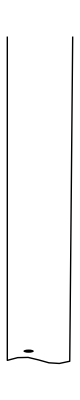

```mathematica
With[{f=Sin},Graphics[{Disk[{2, 3}, 0.5],Line[{{0,100},{0,0},Sequence@@Table[{x,f[x]},{x,0,2π}],{2π,100}}]}]]
```

#### We can use show to put the graphics of the disk with the floor plot. Omega controls the speed at which the sine floor moves, and k controls the frequency of the curves. If the floor looks like chunky lines, set the step size smaller in the floor sequence function below.

```mathematica
Module[{floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,diskR = 0.25,ratio = 0.8,vx,vy,v,numDisks = 5, floorWidth = 10,floorHeight = 20,ω = 1, k = 0.5},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
(*floorV[t_, x_]:=Sin[ω t] Cos[k π  x];*)
(*floorEq[t_,x_]:=floor[t]/floorWidth;*)
floorEqV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorEqV[t, x])]]))];

solns=First@NDSolve[Table[{x[i]''[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤ diskR,
{y[#]'[t]-> 2floorEqV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- ratio x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Animate[
Show[
Graphics[{
{Table[Disk[
Flatten[{Evaluate[x[#][t]/.solns &[i]],Evaluate[If[y[#][t]-floor[t, x[#][t]]< diskR, floor[t, x[#][t]] + diskR, y[#][t]]&[i]/.solns]}],diskR],{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[t, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-1,floorHeight}}}]],{t,tmin,tmax}, AnimationRate->1]
]
```

## Perfecting

#### Because of the time limit, it might not be possible to integrate 3d for now, so we decided to start perfecting the interface of the program.

#### I added friction to the x and y velocities, so it doesn’t keep going forever.

```mathematica
Module[{floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,diskR = 0.25,ratio = 0.8,vx,vy,v,numDisks = 5, floorWidth = 10,floorHeight = 20,ω = 1, k = 0.5, dampingX = 0.02, dampingY =0.01},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤ diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- ratio x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Animate[
Show[
Graphics[{
{Table[Disk[
Flatten[{Evaluate[x[#][t]/.solns &[i]],Evaluate[If[y[#][t]-floor[t, x[#][t]]< diskR, floor[t, x[#][t]] + diskR, y[#][t]]&[i]/.solns]}],diskR],{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[t, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-1,floorHeight}}}]],{t,tmin,tmax}, AnimationRate->1]
]
```

### Colors

```mathematica
Module[{floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,diskR = 0.05,ratio = 0.8,vx,vy,v,numDisks = 5, floorWidth = 10,floorHeight = 20,ω = 1, k = 0.5, dampingX = 0.02, dampingY =0.01},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))+ ArcTan[xt/yt]];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Animate[
Show[
Graphics[{
{Table[{PointSize[(diskR)],Hue[RandomReal[]],Point[
Flatten[{Evaluate[x[#][t]/.solns &[i]],Evaluate[If[y[#][t]-floor[t, x[#][t]]< diskR,floor[t, x[#][t]] + diskR, y[#][t]]&[i]/.solns]}]]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[t, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-1,floorHeight}}}]],{t,tmin,tmax}, AnimationRate->1]
]
```

```mathematica
Module[{floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,diskR = 0.15,ratio = 0.8,vx,vy,v,numDisks = 10, floorWidth = 10,floorHeight = 20,ω = 1, k = 0.5, dampingX = 0.02, dampingY =0.01},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]<= diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Animate[
Show[
Graphics[{
{Table[{Hue[RandomReal[]],Disk[
Flatten[{Evaluate[x[#][t]/.solns &[i]],Evaluate[If[y[#][t]-floor[t, x[#][t]]< diskR, floor[t, x[#][t]] + diskR, y[#][t]]&[i]/.solns]}], diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[t, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-1,floorHeight}}}]],{t,tmin,tmax}, AnimationRate->1]
]
```

### Manipulate

```mathematica
Manipulate[
Module[{floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=2.5,diskR = 0.15,ratio = 0.8,vx,vy,v,numDisks = 2, floorWidth = 10,floorHeight = 15,ω = 1, dampingX = 0.02, dampingY =0.01, colors},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==5,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]<= diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Graphics[{
{Table[{Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],Evaluate[If[y[#][tt]-floor[tt, x[#][tt]]< diskR, floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]/.solns]}], diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-1,floorHeight}}}]
],

{{k,0.5,"wave number"},0.1,1,0.1,Appearance->"Labeled"},
{{tt,0,"time"},0,2.5,ControlType->Trigger},
ContinuousAction->False

]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {True, 2[0] == 1.265148263397407`, True, « 2 », SuperscriptBox[y[1], {« 1 »}.

ReplaceAll::reps: True2[0] == 1.265148263397407`True« 2 »SuperscriptBox[y[1], WhenEvent[y[1][t] - floor$668299[t, x[1][t]] ≤ diskR$668299, {SuperscriptBox[y[1], WhenEvent[x[1][t] ≤ diskR$668299 || x[1][t] ≥ floorWidth$668299 - diskR$668299, SuperscriptBox[x[1],  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: True4[0] == 2.9012080227709216`True« 1 »« 1 »SuperscriptBox[y « 1 » « 1 »], WhenEvent[y[2][t] - floor$668299[t, x[2][t]] ≤ diskR$668299, {SuperscriptBox[y[2], WhenEvent[x[2][t] ≤ diskR$668299 || x[2][t] ≥ floorWidth$668299 - diskR$668299, SuperscriptBox[x[2],  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: True2[0] == 1.265148263397407`True« 2 »SuperscriptBox[y[1], WhenEvent[y[1][t] - floor$668299[t, x[1][t]] ≤ diskR$668299, {SuperscriptBox[y[1], WhenEvent[x[1][t] ≤ diskR$668299 || x[1][t] ≥ floorWidth$668299 - diskR$668299, SuperscriptBox[x[1],  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
Manipulate[Module[{floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,diskR = 0.25,ratio = 0.8,vx,vy,v,numDisks = 5, floorWidth = 10,floorHeight = 20,ω = 1, k = 0.5},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
(*floorV[t_, x_]:=Sin[ω t] Cos[k π  x];*)
(*floorEq[t_,x_]:=floor[t]/floorWidth;*)
floorEqV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorEqV[t, x])]]))];

solns=First@NDSolve[Table[{x[i]''[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤ diskR,
{y[#]'[t]-> 2floorEqV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- ratio x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Animate[
Show[
Graphics[{
{Table[Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],Evaluate[If[y[#][tt]-floor[tt, x[#][tt]]< diskR, floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]/.solns]}],diskR],{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-1,floorHeight}}}]],{t,tmin,tmax}, AnimationRate->1]
],
{{tt,0,"time"},0,2.5,ControlType->Trigger}]
```

### Trajectory Lines

#### Putting in lines that follow the trajectory of each ball.

```mathematica
Module[{colors,floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,diskR = 0.15,ratio = 0.8,vx,vy,v,numDisks = 5, floorWidth = 10,floorHeight = 20,ω = 1, k = 0.5, dampingX = 0.02, dampingY =0.01},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))+ ArcTan[xt/yt]];

colors=ConstantArray[0,numDisks];
Table[(colors[[i]]=ColorData["DarkRainbow"][RandomReal[]]),{i,1,numDisks}];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Manipulate[
Show[
Graphics[Evaluate[{
{Table[{colors[[i]],Line[Table[{x[#][zz],y[#][zz]}&[i],{zz,tmin,tt,(tmax-tmin)/1000.}]],Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],If[y[#][tt]-floor[tt, x[#][tt]]< diskR,floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]}],diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-1,floorHeight}}}/.solns]]],{tt,tmin,tmax,ControlType->Trigger,AnimationRate->0.2}]
]
```

#### Making the lines disappear after a while.

```mathematica
Module[{colors,floor,floorV,solns,tmin=0,tmax=25,diskR = 0.3,ratio = 0.8,vx,vy,v,numDisks = 5, floorWidth = 10,floorHeight = 20,ω = 1, k = 0.5, dampingX = 0.02, dampingY =0.01},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))+ ArcTan[xt/yt]];

colors=ConstantArray[0,numDisks];
Table[(colors[[i]]=ColorData["DarkRainbow"][RandomReal[]]),{i,1,numDisks}];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Manipulate[
Show[
Graphics[Evaluate[{
{Table[{colors[[i]],Line[Table[{x[#][zz],y[#][zz]}&[i],{zz,Max[tmin,tt-(tmax-tmin)/20],tt,(tmax-tmin)/1000.}]],Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],If[y[#][tt]-floor[tt, x[#][tt]]< diskR,floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]}],diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-1,floorHeight}}}/.solns]]],{tt,tmin,tmax,ControlType->Trigger,AnimationRate->0.35}]
]
```

## Form Function Form

#### Attempting to Cloud Deploy

```mathematica
CloudDeploy[
ExportForm[
Module[{colors,floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=7,diskR = 0.15,ratio = 0.8,vx,vy,v,numDisks = 2, floorWidth = 10,floorHeight = 20,ω = 1, k = 0.5, dampingX = 0.02, dampingY =0.01},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))+ ArcTan[xt/yt]];

colors=ConstantArray[0,numDisks];
Table[(colors[[i]]=ColorData["DarkRainbow"][RandomReal[]]),{i,1,numDisks}];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Table[
Graphics[Evaluate[{
{Table[{colors[[i]],Line[Table[{x[#][zz],y[#][zz]}&[i],{zz,Max[tmin,t-(tmax-tmin)/20],t,(tmax-tmin)/1000.}]],Disk[
Flatten[{Evaluate[x[#][t]/.solns &[i]],If[y[#][t]-floor[t, x[#][t]]<= diskR,floor[t, x[#][t]] + diskR, y[#][t]]&[i]}],diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[t, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-2,floorHeight}}}/.solns]],{t,tmin,tmax, 0.1}]]

(*Manipulate[
Show[
Graphics[Evaluate[{
{Table[{colors[[i]],Line[Table[{x[#][zz],y[#][zz]}&[i],{zz,Max[tmin,tt-(tmax-tmin)/20],tt,(tmax-tmin)/1000.}]],Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],If[y[#][tt]-floor[tt, x[#][tt]]<= diskR,floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]}],diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-2,floorHeight}}, PlotRangeClipping-> True}/.solns]]],{tt,tmin,tmax,ControlType->Slider}]*), "GIF"],"BouncingBallSimulation"]
```

CloudObject[]

```mathematica
Clear[bouncing]
```

```mathematica
bouncing[ratio_] :=Module[{colors,floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=4,diskR = 0.15,vx,vy,v,numDisks = 1, floorWidth = 10,floorHeight = 20,ω = 1, k = 0.5, dampingX = 0.02, dampingY =0.01},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))+ ArcTan[xt/yt]];

colors=ConstantArray[0,numDisks];
Table[(colors[[i]]=ColorData["DarkRainbow"][RandomReal[]]),{i,1,numDisks}];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Table[
Graphics[Evaluate[{
{Table[{colors[[i]],Line[Table[{x[#][zz],y[#][zz]}&[i],{zz,Max[tmin,tt-(tmax-tmin)/20],tt,(tmax-tmin)/1000.}]],Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],If[y[#][tt]-floor[tt, x[#][tt]]<= diskR,floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]}],diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}],PlotRange->{{0,floorWidth}, {-2,floorHeight}}}/.solns]],{tt,tmin,tmax, 0.1}]]
```

```mathematica
CloudDeploy[FormFunction[{"ratio"-> "SemanticNumber"},bouncing[#ratio]&,"GIF"], "BouncingBallSimulation"]
```

CloudObject[]

#### IT WORKS!

```mathematica
bouncing[numDisks_, diskR_, k_, colorSchemes_] :=Module[{colors,floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,vx,vy,v,ratio = 0.8, floorWidth = 10,floorHeight = 20,ω = 1, dampingX = 0.02, dampingY =0.01},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))+ ArcTan[xt/yt]];

colors=ConstantArray[0,numDisks];
Table[(colors[[i]]=ColorData[colorSchemes][RandomReal[]]),{i,1,numDisks}];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Table[
Graphics[Evaluate[{
{Table[{colors[[i]],Line[Table[{x[#][zz],y[#][zz]}&[i],{zz,Max[tmin,tt-(tmax-tmin)/20],tt,(tmax-tmin)/1000.}]],Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],If[y[#][tt]-floor[tt, x[#][tt]]<= diskR,floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]}],diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}](*,PlotRange->{{0,floorWidth}, {-2,floorHeight}}*)}/.solns],PlotRange-> {{0, floorWidth+2}, {-2, floorHeight}},PlotRangeClipping->True],{tt,tmin,tmax, 0.1}]]

CloudDeploy[FormFunction[{"numDisks"-> "SemanticNumber", "diskR"-><|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>, "k"-> <|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>, "colorSchemes"-> ColorData["Gradients"]},bouncing[#numDisks, #diskR, #k, #colorSchemes]&,"GIF"], "BouncingBallSimulation"]
```

CloudObject[]

#### Rearranging and more formatting

```mathematica
bouncing[numDisks_, diskR_,colorSchemes_, k_] :=Module[{colors,floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,vx,vy,v,ratio = 0.8, floorWidth = 10,floorHeight = 20,ω = 1, dampingX = 0.5, dampingY =0.1},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))+ ArcTan[xt/yt]];

colors=ConstantArray[0,numDisks];
Table[(colors[[i]]=ColorData[colorSchemes][RandomReal[]]),{i,1,numDisks}];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Table[
Graphics[Evaluate[{
{Table[{colors[[i]],Line[Table[{x[#][zz],y[#][zz]}&[i],{zz,Max[tmin,tt-(tmax-tmin)/20],tt,(tmax-tmin)/1000.}]],Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],If[y[#][tt]-floor[tt, x[#][tt]]<= diskR,floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]}],diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}]}/.solns],PlotRange-> {{-1, floorWidth+2}, {-2, floorHeight+1}},PlotRangeClipping->True],{tt,tmin,tmax, 0.1}]]

CloudDeploy[FormFunction[{"NumberOfDisks"-> <|"Interpreter"-> "SemanticNumber", "Help"-> "The more disks the longer it will take to load!"|>, "DiskRadius"-><|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5, "ColorSchemes"-> ColorData["Gradients"],"Wavelength"-> <|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5},bouncing[#NumberOfDisks, #DiskRadius, #ColorSchemes, #Wavelength]&,"GIF",AppearanceRules-> <|"Title"-> Style["Simulating Particles on a Vibrating Surface", {Bold,Red, 30, FontFamily->"TimeBurner"}],"Description"-> Style["This is a small scale simulation of cymatics, the pattern of sand particles on a vibrational membrane. With different settings and controls, we could control the frequency of nodes on the floor, and change the bounce of the particles accordingly. Hopefully, this project would allow us to visualize sound in interesting ways!", {FontFamily->"Adobe Song Std"}], "SubmitLabel"-> "Let's Go!"|>], "BouncingBallSimulation", Permissions->"Public"]
```

CloudObject[]

#### Final Form

```mathematica
bouncing[numDisks_, diskR_,colorSchemes_, k_] :=Module[{colors,floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,vx,vy,v,ratio = 0.8, floorWidth = 10,floorHeight = 20,ω = 1, dampingX = 0.5, dampingY =0.1},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))+ ArcTan[xt/yt]];

colors=ConstantArray[0,numDisks];
Table[(colors[[i]]=ColorData[colorSchemes][RandomReal[]]),{i,1,numDisks}];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Table[
Graphics[Evaluate[{
{Table[{colors[[i]],Line[Table[{x[#][zz],y[#][zz]}&[i],{zz,Max[tmin,tt-(tmax-tmin)/20],tt,(tmax-tmin)/1000.}]],Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],If[y[#][tt]-floor[tt, x[#][tt]]<= diskR,floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]}],diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}]}/.solns],PlotRange-> {{-1, floorWidth+2}, {-2, floorHeight+1}},PlotRangeClipping->True],{tt,tmin,tmax, 0.1}]]

CloudDeploy[FormFunction[{"NumberOfDisks"-> <|"Interpreter"-> "SemanticNumber", "Help"-> "The more disks the longer it will take to load!"|>, "DiskRadius"-><|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5, "ColorSchemes"-> ColorData["Gradients"],"Wavelength"-> <|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5},bouncing[#NumberOfDisks, #DiskRadius, #ColorSchemes, #Wavelength]&,"GIF",AppearanceRules-> <|"Title"-> Style["Simulating Particles on a Vibrating Surface", {Bold,Red, 30, FontFamily->"TimeBurner"}],"Description"-> Style["This is a small scale simulation of cymatics, the pattern of sand particles on a vibrational membrane. With different settings and controls, we could control the frequency of nodes on the floor, and change the bounce of the particles accordingly. Hopefully, this project would allow us to visualize sound in interesting ways!", {FontFamily->"Adobe Song Std"}], "SubmitLabel"-> "Let's Go!"|>], "BouncingBallSimulation", Permissions->"Public"]
```

CloudObject[]

# 3D

```mathematica
bouncing2[numDisks_,diskR_,colorSchemes_,k_] :=Module[{
dampingX=0.02,
dampingY=0.02,
dampingZ=0.01,
floorWidth=10,
tmin=0,
tmax=10,
ω=1},

δ=floorWidth/20;
grid=N[Table[{x+.01,y+.01},{x,-floorWidth,floorWidth,δ},{y,-floorWidth,floorWidth,δ}]];

floorC=With[{ω=ω,k=k},
Compile[
{{t,_Real},{pt,_Real,1}},
Module[{x=pt⟦1⟧,y=pt⟦2⟧},
Cos[ω t]Sin[k π (√(x^2+y^2))]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
]];

reflectX=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$,V21$,V22$},V1$=px^2;V2$=py^2;V3$=1/2;V4$=Cos[t];V5$=V1$+V2$;V6$=V5$^V3$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V4$^2;V10$=V8$^2;V11$=2.4674011002723395 V10$ V9$;V12$=V4$^4;V13$=px V4$ V8$;V14$=py V4$ V8$;V15$=Abs[V13$];V16$=Abs[V14$];V17$=V8$^4;V18$=1.+V11$;V19$=-0.5 V10$ V9$;V20$=V15$^2;V21$=V16$^2;V22$=-0.20264236728467558+V19$;-((4.934802200544678 (-0.08212785803747472 V1$ vx+1. V1$ V12$ V17$ vx-0.08212785803747472 V2$ vx+V20$ V22$ vx+V21$ V22$ vx+0.20264236728467558 V1$ V10$ V9$ vx-0.20264236728467558 V10$ V2$ V9$ vx+1. px py V12$ V17$ vy+0.40528473456935116 px py V10$ V9$ vy-0.258012275465596 V13$ vz ((1+V11$) (V5$+(2.4674011002723395 V1$+2.4674011002723395 V2$) V9$ Cos[1.5707963267948966 (V1$+V2$)^V3$]^2))^V3$))/(0.4052847345693511 V1$+0.4052847345693511 V2$+V18$ V20$+V18$ V21$+1. V1$ V10$ V9$+1. V10$ V2$ V9$))]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

reflectY=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$},V1$=py^2;V2$=px^2;V3$=1/2;V4$=Cos[t];V5$=V1$+V2$;V6$=V5$^V3$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V4$^2;V10$=V8$^2;V11$=2.467401100272339 V10$ V9$;V12$=1.+V11$;V13$=px V4$ V8$;V14$=py V4$ V8$;V15$=Abs[V13$];V16$=Abs[V14$];V17$=V15$^2;V18$=V16$^2;V19$=V4$^4;V20$=V8$^4;(1. (-4.934802200544678 px py V19$ V20$ vx-2. px py V10$ V9$ vx+0.4052847345693511 V1$ vy+V12$ V17$ vy+V12$ V18$ vy+0.4052847345693511 V2$ vy-4.934802200544678 V1$ V19$ V20$ vy-1. V1$ V10$ V9$ vy+1. V10$ V2$ V9$ vy+1.2732395447351628 V14$ vz ((1+V11$) (V5$+(2.4674011002723395 V1$+2.4674011002723395 V2$) V9$ Cos[1.5707963267948966 (V1$+V2$)^V3$]^2))^V3$))/(0.4052847345693511 V1$+V12$ V17$+V12$ V18$+0.4052847345693511 V2$+1. V1$ V10$ V9$+1. V10$ V2$ V9$)]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

reflectZ=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$,V21$,V22$,V23$,V24$,V25$,V26$,V27$,V28$,V29$,V30$,V31$,V32$,V33$},V1$=px^2;V2$=py^2;V3$=V1$+V2$;V4$=1/2;V5$=Cos[t];V6$=V3$^V4$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V5$^2;V10$=V8$^2;V11$=2.4674011002723395 V10$ V9$;V12$=1+V11$;V13$=V1$+V2$;V14$=V13$^V4$;V15$=1.5707963267948966 V14$;V16$=Cos[V15$];V17$=2.4674011002723395 V1$;V18$=V16$^2;V19$=2.4674011002723395 V2$;V20$=V17$+V19$;V21$=V18$ V20$ V9$;V22$=V21$+V3$;V23$=-1/2;V24$=px V5$ V8$;V25$=py V5$ V8$;V26$=Abs[V24$];V27$=Abs[V25$];V28$=V26$^2;V29$=V27$^2;V30$=V22$^V23$;V31$=3/2;V32$=V12$^V31$;V33$=1/V22$;(V12$^V23$ V3$ (1.2732395447351628 V12$ V24$ V30$ vx+1.2732395447351628 V12$ V25$ V30$ vy-0.4052847345693511 V12$^V4$ vz+1. V28$ V32$ V33$ vz+1. V29$ V32$ V33$ vz))/(0.4052847345693511 V1$+0.4052847345693511 V2$+1. V28$+1. V29$)]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

solution[{x0_,y0_,z0_}]:=Module[
{x,y,z,solns},
solns=First[Quiet@NDSolve[{
x''[t]+dampingX x'[t]== 0,
x[0]== x0,
x'[0]==0.0,

y''[t]+dampingY y'[t]== 0,
y[0]==y0,
y'[0]==0.0,

z''[t]+dampingZ z'[t]==-9.81,
z[0]==z0,
z'[0]==0,

WhenEvent[z[t]≤floorC[t,{x[t],y[t]}] +diskR,{
z[t]->floorC[t,{x[t],y[t]}]+diskR+.05,
x'[t]->reflectX[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}],
y'[t]->reflectY[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}],
z'[t]->reflectZ[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}]
}],

WhenEvent[x[t]≤-floorWidth+diskR,x'[t]->Abs[x'[t]]],
WhenEvent[y[t]≤-floorWidth+diskR,y'[t]->Abs[y'[t]]],
WhenEvent[x[t]≥floorWidth-diskR,x'[t]->-Abs[x'[t]]],
WhenEvent[y[t]≥floorWidth-diskR,y'[t]->-Abs[y'[t]]]
},
{x,y,z},
{t,0.0,25.0},WorkingPrecision->8
]];
Evaluate[{x[#],y[#],z[#]}/.solns]&
];

initialPositions=MapAt[Abs[#]+5&,RandomReal[{-5,5},{numDisks,3}],{All,3}];
functions=solution/@initialPositions;

Table[
Show[Graphics3D[{Gray,
Line[Table[#[t0],{t0,tt-.25,tt,.05}]],
Sphere[#[tt],diskR]
}&/@functions],
ListPlot3D[floorC[tt,grid],
DataRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth}},
PlotRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth},{-1,10}},
PerformanceGoal->"Quality", Mesh-> None, ColorFunction-> colorSchemes
],
PlotRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth},{-1,10}}
],
{tt,tmin+0.1,tmax, 0.01}
]
]
```

```mathematica
CloudDeploy[FormFunction[{"NumberOfDisks"-> <|"Interpreter"-> "SemanticNumber", "Help"-> "The more disks the longer it will take to load!"|>, "DiskRadius"-><|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5, "ColorSchemes"-> ColorData["Gradients"],"Wavelength"-> <|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5},bouncing2[#NumberOfDisks, #DiskRadius, #ColorSchemes, #Wavelength]&,"GIF",AppearanceRules-> <|"Title"-> Style["Simulating Particles on a Vibrating Surface (3D)", {Bold,Red, 30, FontFamily->"TimeBurner"}],"Description"-> Style["This is a small scale simulation of cymatics, the pattern of sand particles on a vibrational membrane. With different settings and controls, we could control the frequency of nodes on the floor, and change the bounce of the particles accordingly. Hopefully, this project would allow us to visualize sound in interesting ways!", {FontFamily->"Adobe Song Std"}], "SubmitLabel"-> "Let's Go!"|>], "BouncingBallSimulation3D", Permissions->"Public"]
```

CloudObject[]

```mathematica
bouncing2[numDisks_, diskR_, colorSchemes_, k_]:= Module[{
dampingX=0.02,
dampingY=0.02,
dampingZ=0.01,
floorWidth=10,
tmin=0,
tmax=10,
ω=1},

δ=floorWidth/20;
grid=N[Table[{x+.01,y+.01},{x,-floorWidth,floorWidth,δ},{y,-floorWidth,floorWidth,δ}]];

floorC=With[{w=ω,kk=k},
Compile[
{{t,_Real},{pt,_Real,1}},
Module[{x=pt⟦1⟧,y=pt⟦2⟧},
Cos[w t]Sin[kk π (√(x^2+y^2))]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
]];

reflectX=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$,V21$,V22$},V1$=px^2;V2$=py^2;V3$=1/2;V4$=Cos[t];V5$=V1$+V2$;V6$=V5$^V3$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V4$^2;V10$=V8$^2;V11$=2.4674011002723395 V10$ V9$;V12$=V4$^4;V13$=px V4$ V8$;V14$=py V4$ V8$;V15$=Abs[V13$];V16$=Abs[V14$];V17$=V8$^4;V18$=1.+V11$;V19$=-0.5 V10$ V9$;V20$=V15$^2;V21$=V16$^2;V22$=-0.20264236728467558+V19$;-((4.934802200544678 (-0.08212785803747472 V1$ vx+1. V1$ V12$ V17$ vx-0.08212785803747472 V2$ vx+V20$ V22$ vx+V21$ V22$ vx+0.20264236728467558 V1$ V10$ V9$ vx-0.20264236728467558 V10$ V2$ V9$ vx+1. px py V12$ V17$ vy+0.40528473456935116 px py V10$ V9$ vy-0.258012275465596 V13$ vz ((1+V11$) (V5$+(2.4674011002723395 V1$+2.4674011002723395 V2$) V9$ Cos[1.5707963267948966 (V1$+V2$)^V3$]^2))^V3$))/(0.4052847345693511 V1$+0.4052847345693511 V2$+V18$ V20$+V18$ V21$+1. V1$ V10$ V9$+1. V10$ V2$ V9$))]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

reflectY=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$},V1$=py^2;V2$=px^2;V3$=1/2;V4$=Cos[t];V5$=V1$+V2$;V6$=V5$^V3$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V4$^2;V10$=V8$^2;V11$=2.467401100272339 V10$ V9$;V12$=1.+V11$;V13$=px V4$ V8$;V14$=py V4$ V8$;V15$=Abs[V13$];V16$=Abs[V14$];V17$=V15$^2;V18$=V16$^2;V19$=V4$^4;V20$=V8$^4;(1. (-4.934802200544678 px py V19$ V20$ vx-2. px py V10$ V9$ vx+0.4052847345693511 V1$ vy+V12$ V17$ vy+V12$ V18$ vy+0.4052847345693511 V2$ vy-4.934802200544678 V1$ V19$ V20$ vy-1. V1$ V10$ V9$ vy+1. V10$ V2$ V9$ vy+1.2732395447351628 V14$ vz ((1+V11$) (V5$+(2.4674011002723395 V1$+2.4674011002723395 V2$) V9$ Cos[1.5707963267948966 (V1$+V2$)^V3$]^2))^V3$))/(0.4052847345693511 V1$+V12$ V17$+V12$ V18$+0.4052847345693511 V2$+1. V1$ V10$ V9$+1. V10$ V2$ V9$)]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

reflectZ=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$,V21$,V22$,V23$,V24$,V25$,V26$,V27$,V28$,V29$,V30$,V31$,V32$,V33$},V1$=px^2;V2$=py^2;V3$=V1$+V2$;V4$=1/2;V5$=Cos[t];V6$=V3$^V4$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V5$^2;V10$=V8$^2;V11$=2.4674011002723395 V10$ V9$;V12$=1+V11$;V13$=V1$+V2$;V14$=V13$^V4$;V15$=1.5707963267948966 V14$;V16$=Cos[V15$];V17$=2.4674011002723395 V1$;V18$=V16$^2;V19$=2.4674011002723395 V2$;V20$=V17$+V19$;V21$=V18$ V20$ V9$;V22$=V21$+V3$;V23$=-1/2;V24$=px V5$ V8$;V25$=py V5$ V8$;V26$=Abs[V24$];V27$=Abs[V25$];V28$=V26$^2;V29$=V27$^2;V30$=V22$^V23$;V31$=3/2;V32$=V12$^V31$;V33$=1/V22$;(V12$^V23$ V3$ (1.2732395447351628 V12$ V24$ V30$ vx+1.2732395447351628 V12$ V25$ V30$ vy-0.4052847345693511 V12$^V4$ vz+1. V28$ V32$ V33$ vz+1. V29$ V32$ V33$ vz))/(0.4052847345693511 V1$+0.4052847345693511 V2$+1. V28$+1. V29$)]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];
solution[{x0_,y0_,z0_}]:=Module[
{x,y,z,solns},
solns=First[Quiet@NDSolve[{
x''[t]+dampingX x'[t]== 0,
x[0]== x0,
x'[0]==0.0,

y''[t]+dampingY y'[t]== 0,
y[0]==y0,
y'[0]==0.0,

z''[t]+dampingZ z'[t]==-9.81,
z[0]==z0,
z'[0]==0,

WhenEvent[z[t]≤floorC[t,{x[t],y[t]}] +diskR,{
z[t]->floorC[t,{x[t],y[t]}]+diskR+.05,
x'[t]->reflectX[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}],
y'[t]->reflectY[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}],
z'[t]->reflectZ[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}]
}],

WhenEvent[x[t]≤-floorWidth+diskR,x'[t]->Abs[x'[t]]],
WhenEvent[y[t]≤-floorWidth+diskR,y'[t]->Abs[y'[t]]],
WhenEvent[x[t]≥floorWidth-diskR,x'[t]->-Abs[x'[t]]],
WhenEvent[y[t]≥floorWidth-diskR,y'[t]->-Abs[y'[t]]]
},
{x,y,z},
{t,0.0,25.0},WorkingPrecision->8
]];
Evaluate[{x[#],y[#],z[#]}/.solns]&
];

initialPositions=MapAt[Abs[#]+5&,RandomReal[{-5,5},{numDisks,3}],{All,3}];
functions=solution/@initialPositions;

Table[
Show[Graphics3D[{Red,
Line[Table[#[t0],{t0,tt-.25,tt,.05}]],
Sphere[#[tt],diskR]
}&/@functions],
ListPlot3D[floorC[tt,grid],
DataRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth}},
PlotRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth},{-1,10}},
PerformanceGoal->"Quality", Mesh-> None, ColorFunction->colorSchemes
],
PlotRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth},{-1,10}}
],
{tt,tmin+.25,tmax}
]
]

CloudDeploy[FormFunction[{"NumberOfDisks"-> <|"Interpreter"-> "SemanticNumber", "Help"-> "The more disks the longer it will take to load!"|>, "DiskRadius"-><|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5, "ColorSchemes"-> ColorData["Gradients"],"Wavelength"-> <|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5},bouncing2[#NumberOfDisks, #DiskRadius, #ColorSchemes, #Wavelength]&,"GIF",AppearanceRules-> <|"Title"-> Style["Simulating Particles on a Vibrating Surface(3D)", {Bold,Red, 30, FontFamily->"TimeBurner"}],"Description"-> Style["This is a small scale simulation of cymatics, the pattern of sand particles on a vibrational membrane. With different settings and controls, we could control the frequency of nodes on the floor, and change the bounce of the particles accordingly. Hopefully, this project would allow us to visualize sound in interesting ways!", {FontFamily->"Adobe Song Std"}], "SubmitLabel"-> "Let's Go!"|>], "BouncingBallSimulation3D", Permissions->"Public"]
```

CloudObject[]

#### Final Projects

### 2D

```mathematica
bouncing[numDisks_, diskR_,colorSchemes_, k_] :=Module[{colors,floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,vx,vy,v,ratio = 0.8, floorWidth = 10,floorHeight = 20,ω = 1, dampingX = 0.5, dampingY =0.1},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))+ ArcTan[xt/yt]];

colors=ConstantArray[0,numDisks];
Table[(colors[[i]]=ColorData[colorSchemes][RandomReal[]]),{i,1,numDisks}];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Table[
Graphics[Evaluate[{
{Table[{colors[[i]],Line[Table[{x[#][zz],y[#][zz]}&[i],{zz,Max[tmin,tt-(tmax-tmin)/20],tt,(tmax-tmin)/1000.}]],Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],If[y[#][tt]-floor[tt, x[#][tt]]<= diskR,floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]}],diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}]}/.solns],PlotRange-> {{-1, floorWidth+2}, {-2, floorHeight+1}},PlotRangeClipping->True],{tt,tmin,tmax, 0.1}]]

CloudDeploy[FormFunction[{"NumberOfDisks"-> <|"Interpreter"-> "Integer", "Help"-> "The more disks the longer it will take to load!"|>, "DiskRadius"-><|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5, "ColorSchemes"-> ColorData["Gradients"],"Wavelength"-> <|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5},bouncing[#NumberOfDisks, #DiskRadius, #ColorSchemes, #Wavelength]&,"GIF",AppearanceRules-> <|"Title"-> Style["Simulating Particles on a Vibrating Surface", {Bold,Red, 30, FontFamily->"TimeBurner"}],"Description"-> Style["This is a small scale simulation of cymatics, the pattern of sand particles on a vibrational membrane. With different settings and controls, we could control the frequency of nodes on the floor, and change the bounce of the particles accordingly. Hopefully, this project would allow us to visualize sound in interesting ways!", {FontFamily->"Adobe Song Std"}], "SubmitLabel"-> "Let's Go!"|>], "BouncingBallSimulation", Permissions->"Public"]
```

CloudObject[]

#### 3D

```mathematica
bouncing2[numDisks_,diskR_,colorSchemes_,k_] :=Module[{
dampingX=0.02,
dampingY=0.02,
dampingZ=0.01,
floorWidth=10,
tmin=0,
tmax=10,
ω=1},

δ=floorWidth/20;
grid=N[Table[{x+.01,y+.01},{x,-floorWidth,floorWidth,δ},{y,-floorWidth,floorWidth,δ}]];

floorC=With[{w=ω,kk=k},
Compile[
{{t,_Real},{pt,_Real,1}},
Module[{x=pt⟦1⟧,y=pt⟦2⟧},
Cos[w t]Sin[kk π (√(x^2+y^2))]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
]];

reflectX=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$,V21$,V22$},V1$=px^2;V2$=py^2;V3$=1/2;V4$=Cos[t];V5$=V1$+V2$;V6$=V5$^V3$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V4$^2;V10$=V8$^2;V11$=2.4674011002723395 V10$ V9$;V12$=V4$^4;V13$=px V4$ V8$;V14$=py V4$ V8$;V15$=Abs[V13$];V16$=Abs[V14$];V17$=V8$^4;V18$=1.+V11$;V19$=-0.5 V10$ V9$;V20$=V15$^2;V21$=V16$^2;V22$=-0.20264236728467558+V19$;-((4.934802200544678 (-0.08212785803747472 V1$ vx+1. V1$ V12$ V17$ vx-0.08212785803747472 V2$ vx+V20$ V22$ vx+V21$ V22$ vx+0.20264236728467558 V1$ V10$ V9$ vx-0.20264236728467558 V10$ V2$ V9$ vx+1. px py V12$ V17$ vy+0.40528473456935116 px py V10$ V9$ vy-0.258012275465596 V13$ vz ((1+V11$) (V5$+(2.4674011002723395 V1$+2.4674011002723395 V2$) V9$ Cos[1.5707963267948966 (V1$+V2$)^V3$]^2))^V3$))/(0.4052847345693511 V1$+0.4052847345693511 V2$+V18$ V20$+V18$ V21$+1. V1$ V10$ V9$+1. V10$ V2$ V9$))]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

reflectY=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$},V1$=py^2;V2$=px^2;V3$=1/2;V4$=Cos[t];V5$=V1$+V2$;V6$=V5$^V3$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V4$^2;V10$=V8$^2;V11$=2.467401100272339 V10$ V9$;V12$=1.+V11$;V13$=px V4$ V8$;V14$=py V4$ V8$;V15$=Abs[V13$];V16$=Abs[V14$];V17$=V15$^2;V18$=V16$^2;V19$=V4$^4;V20$=V8$^4;(1. (-4.934802200544678 px py V19$ V20$ vx-2. px py V10$ V9$ vx+0.4052847345693511 V1$ vy+V12$ V17$ vy+V12$ V18$ vy+0.4052847345693511 V2$ vy-4.934802200544678 V1$ V19$ V20$ vy-1. V1$ V10$ V9$ vy+1. V10$ V2$ V9$ vy+1.2732395447351628 V14$ vz ((1+V11$) (V5$+(2.4674011002723395 V1$+2.4674011002723395 V2$) V9$ Cos[1.5707963267948966 (V1$+V2$)^V3$]^2))^V3$))/(0.4052847345693511 V1$+V12$ V17$+V12$ V18$+0.4052847345693511 V2$+1. V1$ V10$ V9$+1. V10$ V2$ V9$)]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

reflectZ=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$,V21$,V22$,V23$,V24$,V25$,V26$,V27$,V28$,V29$,V30$,V31$,V32$,V33$},V1$=px^2;V2$=py^2;V3$=V1$+V2$;V4$=1/2;V5$=Cos[t];V6$=V3$^V4$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V5$^2;V10$=V8$^2;V11$=2.4674011002723395 V10$ V9$;V12$=1+V11$;V13$=V1$+V2$;V14$=V13$^V4$;V15$=1.5707963267948966 V14$;V16$=Cos[V15$];V17$=2.4674011002723395 V1$;V18$=V16$^2;V19$=2.4674011002723395 V2$;V20$=V17$+V19$;V21$=V18$ V20$ V9$;V22$=V21$+V3$;V23$=-1/2;V24$=px V5$ V8$;V25$=py V5$ V8$;V26$=Abs[V24$];V27$=Abs[V25$];V28$=V26$^2;V29$=V27$^2;V30$=V22$^V23$;V31$=3/2;V32$=V12$^V31$;V33$=1/V22$;(V12$^V23$ V3$ (1.2732395447351628 V12$ V24$ V30$ vx+1.2732395447351628 V12$ V25$ V30$ vy-0.4052847345693511 V12$^V4$ vz+1. V28$ V32$ V33$ vz+1. V29$ V32$ V33$ vz))/(0.4052847345693511 V1$+0.4052847345693511 V2$+1. V28$+1. V29$)]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

solution[{x0_,y0_,z0_}]:=Module[
{x,y,z,solns},
solns=First[Quiet@NDSolve[{
x''[t]+dampingX x'[t]== 0,
x[0]== x0,
x'[0]==0.0,

y''[t]+dampingY y'[t]== 0,
y[0]==y0,
y'[0]==0.0,

z''[t]+dampingZ z'[t]==-9.81,
z[0]==z0,
z'[0]==0,

WhenEvent[z[t]≤floorC[t,{x[t],y[t]}] +diskR,{
z[t]->floorC[t,{x[t],y[t]}]+diskR+.05,
x'[t]->reflectX[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}],
y'[t]->reflectY[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}],
z'[t]->reflectZ[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}]
}],

WhenEvent[x[t]≤-floorWidth+diskR,x'[t]->Abs[x'[t]]],
WhenEvent[y[t]≤-floorWidth+diskR,y'[t]->Abs[y'[t]]],
WhenEvent[x[t]≥floorWidth-diskR,x'[t]->-Abs[x'[t]]],
WhenEvent[y[t]≥floorWidth-diskR,y'[t]->-Abs[y'[t]]]
},
{x,y,z},
{t,0.0,25.0},WorkingPrecision->8
]];
Evaluate[{x[#],y[#],z[#]}/.solns]&
];

initialPositions=MapAt[Abs[#]+5&,RandomReal[{-5,5},{numDisks,3}],{All,3}];
functions=solution/@initialPositions;

Table[
Show[Graphics3D[{Gray,
Line[Table[#[t0],{t0,tt-.25,tt,.05}]],
Sphere[#[tt],diskR]
}&/@functions],
ListPlot3D[floorC[tt,grid],
DataRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth}},
PlotRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth},{-1,10}},
PerformanceGoal->"Quality", Mesh-> None, ColorFunction-> colorSchemes
],
PlotRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth},{-1,10}}
],
{tt,tmin+0.25,tmax, 0.1}
]
]

CloudDeploy[FormFunction[{"NumberOfDisks"-> <|"Interpreter"-> "SemanticNumber", "Help"-> "The more disks the longer it will take to load!"|>, "DiskRadius"-><|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5, "ColorSchemes"-> ColorData["Gradients"],"Wavelength"-> <|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5},bouncing2[#NumberOfDisks, #DiskRadius, #ColorSchemes, #Wavelength]&,"GIF",AppearanceRules-> <|"Title"-> Style["Simulating Particles on a Vibrating Surface (3D)", {Bold,Red, 30, FontFamily->"TimeBurner"}],"Description"-> Style["This is a small scale simulation of cymatics, the pattern of sand particles on a vibrational membrane. With different settings and controls, we could control the frequency of nodes on the floor, and change the bounce of the particles accordingly. Hopefully, this project would allow us to visualize sound in interesting ways!", {FontFamily->"Adobe Song Std"}], "SubmitLabel"-> "Let's Go!"|>], "BouncingBallSimulation3D", Permissions->"Public"]
```

CloudObject[]

```mathematica
bouncing2[numDisks_,diskR_,colorSchemes_,k_] :=Module[{
dampingX=0.02,
dampingY=0.02,
dampingZ=0.01,
floorWidth=10,
tmin=0,
tmax=10,
ω=1},

δ=floorWidth/20;
grid=N[Table[{x+.01,y+.01},{x,-floorWidth,floorWidth,δ},{y,-floorWidth,floorWidth,δ}]];

floorC=With[{w=ω,kk=k},
Compile[
{{t,_Real},{pt,_Real,1}},
Module[{x=pt⟦1⟧,y=pt⟦2⟧},
Cos[w t]Sin[kk π (√(x^2+y^2))]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
]];

reflectX=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$,V21$,V22$},V1$=px^2;V2$=py^2;V3$=1/2;V4$=Cos[t];V5$=V1$+V2$;V6$=V5$^V3$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V4$^2;V10$=V8$^2;V11$=2.4674011002723395 V10$ V9$;V12$=V4$^4;V13$=px V4$ V8$;V14$=py V4$ V8$;V15$=Abs[V13$];V16$=Abs[V14$];V17$=V8$^4;V18$=1.+V11$;V19$=-0.5 V10$ V9$;V20$=V15$^2;V21$=V16$^2;V22$=-0.20264236728467558+V19$;-((4.934802200544678 (-0.08212785803747472 V1$ vx+1. V1$ V12$ V17$ vx-0.08212785803747472 V2$ vx+V20$ V22$ vx+V21$ V22$ vx+0.20264236728467558 V1$ V10$ V9$ vx-0.20264236728467558 V10$ V2$ V9$ vx+1. px py V12$ V17$ vy+0.40528473456935116 px py V10$ V9$ vy-0.258012275465596 V13$ vz ((1+V11$) (V5$+(2.4674011002723395 V1$+2.4674011002723395 V2$) V9$ Cos[1.5707963267948966 (V1$+V2$)^V3$]^2))^V3$))/(0.4052847345693511 V1$+0.4052847345693511 V2$+V18$ V20$+V18$ V21$+1. V1$ V10$ V9$+1. V10$ V2$ V9$))]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

reflectY=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$},V1$=py^2;V2$=px^2;V3$=1/2;V4$=Cos[t];V5$=V1$+V2$;V6$=V5$^V3$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V4$^2;V10$=V8$^2;V11$=2.467401100272339 V10$ V9$;V12$=1.+V11$;V13$=px V4$ V8$;V14$=py V4$ V8$;V15$=Abs[V13$];V16$=Abs[V14$];V17$=V15$^2;V18$=V16$^2;V19$=V4$^4;V20$=V8$^4;(1. (-4.934802200544678 px py V19$ V20$ vx-2. px py V10$ V9$ vx+0.4052847345693511 V1$ vy+V12$ V17$ vy+V12$ V18$ vy+0.4052847345693511 V2$ vy-4.934802200544678 V1$ V19$ V20$ vy-1. V1$ V10$ V9$ vy+1. V10$ V2$ V9$ vy+1.2732395447351628 V14$ vz ((1+V11$) (V5$+(2.4674011002723395 V1$+2.4674011002723395 V2$) V9$ Cos[1.5707963267948966 (V1$+V2$)^V3$]^2))^V3$))/(0.4052847345693511 V1$+V12$ V17$+V12$ V18$+0.4052847345693511 V2$+1. V1$ V10$ V9$+1. V10$ V2$ V9$)]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

reflectZ=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$,V21$,V22$,V23$,V24$,V25$,V26$,V27$,V28$,V29$,V30$,V31$,V32$,V33$},V1$=px^2;V2$=py^2;V3$=V1$+V2$;V4$=1/2;V5$=Cos[t];V6$=V3$^V4$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V5$^2;V10$=V8$^2;V11$=2.4674011002723395 V10$ V9$;V12$=1+V11$;V13$=V1$+V2$;V14$=V13$^V4$;V15$=1.5707963267948966 V14$;V16$=Cos[V15$];V17$=2.4674011002723395 V1$;V18$=V16$^2;V19$=2.4674011002723395 V2$;V20$=V17$+V19$;V21$=V18$ V20$ V9$;V22$=V21$+V3$;V23$=-1/2;V24$=px V5$ V8$;V25$=py V5$ V8$;V26$=Abs[V24$];V27$=Abs[V25$];V28$=V26$^2;V29$=V27$^2;V30$=V22$^V23$;V31$=3/2;V32$=V12$^V31$;V33$=1/V22$;(V12$^V23$ V3$ (1.2732395447351628 V12$ V24$ V30$ vx+1.2732395447351628 V12$ V25$ V30$ vy-0.4052847345693511 V12$^V4$ vz+1. V28$ V32$ V33$ vz+1. V29$ V32$ V33$ vz))/(0.4052847345693511 V1$+0.4052847345693511 V2$+1. V28$+1. V29$)]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

solution[{x0_,y0_,z0_}]:=Module[
{x,y,z,solns},
solns=First[Quiet@NDSolve[{
x''[t]+dampingX x'[t]== 0,
x[0]== x0,
x'[0]==0.0,

y''[t]+dampingY y'[t]== 0,
y[0]==y0,
y'[0]==0.0,

z''[t]+dampingZ z'[t]==-9.81,
z[0]==z0,
z'[0]==0,

WhenEvent[z[t]≤floorC[t,{x[t],y[t]}] +diskR,{
z[t]->floorC[t,{x[t],y[t]}]+diskR+.05,
x'[t]->reflectX[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}],
y'[t]->reflectY[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}],
z'[t]->reflectZ[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}]
}],

WhenEvent[x[t]≤-floorWidth+diskR,x'[t]->Abs[x'[t]]],
WhenEvent[y[t]≤-floorWidth+diskR,y'[t]->Abs[y'[t]]],
WhenEvent[x[t]≥floorWidth-diskR,x'[t]->-Abs[x'[t]]],
WhenEvent[y[t]≥floorWidth-diskR,y'[t]->-Abs[y'[t]]]
},
{x,y,z},
{t,0.0,25.0},WorkingPrecision->8
]];
Evaluate[{x[#],y[#],z[#]}/.solns]&
];

initialPositions=MapAt[Abs[#]+5&,RandomReal[{-5,5},{numDisks,3}],{All,3}];
functions=solution/@initialPositions;

Table[
Show[Graphics3D[{Gray,
Line[Table[#[t0],{t0,tt-.25,tt,.05}]],
Sphere[#[tt],diskR]
}&/@functions],
ListPlot3D[floorC[tt,grid],
DataRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth}},
PlotRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth},{-1,10}},
PerformanceGoal->"Quality", Mesh-> None, ColorFunction-> colorSchemes
],
PlotRange->{{-floorWidth,floorWidth+2},{-floorWidth,floorWidth+2},{-1,10}}
],
{tt,tmin+0.25,tmax, 0.1}
]
]

CloudDeploy[FormFunction[{"NumberOfDisks"-> <|"Interpreter"-> "Integer", "Help"-> "The more disks the longer it will take to load!"|>, "DiskRadius"-><|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5, "ColorSchemes"-> ColorData["Gradients"],"Wavelength"-> <|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5},bouncing2[#NumberOfDisks, #DiskRadius, #ColorSchemes, #Wavelength]&,"GIF",AppearanceRules-> <|"Title"-> Style["Simulating Particles on a Vibrating Surface (3D)", {Bold,Red, 30, FontFamily->"TimeBurner"}],"Description"-> Style["This is a small scale simulation of cymatics, the pattern of sand particles on a vibrational membrane. With different settings and controls, we could control the frequency of nodes on the floor, and change the bounce of the particles accordingly. Hopefully, this project would allow us to visualize sound in interesting ways!", {FontFamily->"Adobe Song Std"}], "SubmitLabel"-> "Let's Go!"|>], "BouncingBallSimulation3D", Permissions->"Public"]
```

CloudObject[]

### Put Them Together

```mathematica
bouncing[numDisks_, diskR_,colorSchemes_, k_] :=Module[{colors,floor,floorV,floorEq,floorEqV,solns,tmin=0,tmax=25,vx,vy,v,ratio = 0.8, floorWidth = 10,floorHeight = 20,ω = 1, dampingX = 0.5, dampingY =0.1},

floor[t_, x_] :=Cos[ω t]Sin[k π x];
floorV[t_,x_]:=(D[floor[t,xx],xx]/.xx->x);
v[xt_,yt_] := Sqrt[xt^2+yt^2];
vx[xt_,yt_,t_,x_,y_] := v[xt,yt]Cos[2*(90-(VectorAngle[AngleVector[90- v[xt, yt]],AngleVector[90-(floorV[t, x])]]))+ ArcTan[xt/yt]];

colors=ConstantArray[0,numDisks];
Table[(colors[[i]]=ColorData[colorSchemes][RandomReal[]]),{i,1,numDisks}];

solns=First@NDSolve[Table[{x[i]''[t]+dampingX x[i]'[t]== 0,x[i][0]== RandomReal[{diskR,(floorWidth-diskR)}],x[i]'[0] == 0,
y[i]''[t]+dampingY y[i]'[t]==-9.81,y[i][0]==10,y[i]'[0]==0,
WhenEvent[y[#][t]-floor[t,x[#][t]]≤diskR,
{y[#]'[t]-> 2floorV[t,x[#][t]]-ratio y[#]'[t] ,x[#]'[t]->vx[x[#]'[t], y[#]'[t], t, x[#][t], y[#][t]]}]&[i],
WhenEvent[(x[#][t]≤ diskR|| x[#][t]≥ (floorWidth-diskR)),
x[#]'[t]->- x[#]'[t]] &[i]},{i , 1, numDisks}],Flatten@{Table[x[i],{i,1,numDisks}],Table[y[i],{i,1,numDisks}]},{t,tmin,tmax}];

Table[
Graphics[Evaluate[{
{Table[{colors[[i]],Line[Table[{x[#][zz],y[#][zz]}&[i],{zz,Max[tmin,tt-(tmax-tmin)/20],tt,(tmax-tmin)/1000.}]],Disk[
Flatten[{Evaluate[x[#][tt]/.solns &[i]],If[y[#][tt]-floor[tt, x[#][tt]]<= diskR,floor[tt, x[#][tt]] + diskR, y[#][tt]]&[i]}],diskR]},{i, 1, numDisks}]},Line[{{0,floorHeight},{0,0},Sequence@@Table[{x,floor[tt, x]},{x,0, floorWidth, 0.1}],{floorWidth,floorHeight}}]}/.solns],PlotRange-> {{-1, floorWidth+2}, {-2, floorHeight+1}},PlotRangeClipping->True],{tt,tmin,tmax, 0.1}]]
```

```mathematica
bouncing2[numDisks_,diskR_,colorSchemes_,k_] :=Module[{
dampingX=0.02,
dampingY=0.02,
dampingZ=0.01,
floorWidth=10,
tmin=0,
tmax=10,
ω=1},

δ=floorWidth/20;
grid=N[Table[{x+.01,y+.01},{x,-floorWidth,floorWidth,δ},{y,-floorWidth,floorWidth,δ}]];

floorC=With[{w=ω,kk=k},
Compile[
{{t,_Real},{pt,_Real,1}},
Module[{x=pt⟦1⟧,y=pt⟦2⟧},
Cos[w t]Sin[kk π (√(x^2+y^2))]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
]];

reflectX=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$,V21$,V22$},V1$=px^2;V2$=py^2;V3$=1/2;V4$=Cos[t];V5$=V1$+V2$;V6$=V5$^V3$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V4$^2;V10$=V8$^2;V11$=2.4674011002723395 V10$ V9$;V12$=V4$^4;V13$=px V4$ V8$;V14$=py V4$ V8$;V15$=Abs[V13$];V16$=Abs[V14$];V17$=V8$^4;V18$=1.+V11$;V19$=-0.5 V10$ V9$;V20$=V15$^2;V21$=V16$^2;V22$=-0.20264236728467558+V19$;-((4.934802200544678 (-0.08212785803747472 V1$ vx+1. V1$ V12$ V17$ vx-0.08212785803747472 V2$ vx+V20$ V22$ vx+V21$ V22$ vx+0.20264236728467558 V1$ V10$ V9$ vx-0.20264236728467558 V10$ V2$ V9$ vx+1. px py V12$ V17$ vy+0.40528473456935116 px py V10$ V9$ vy-0.258012275465596 V13$ vz ((1+V11$) (V5$+(2.4674011002723395 V1$+2.4674011002723395 V2$) V9$ Cos[1.5707963267948966 (V1$+V2$)^V3$]^2))^V3$))/(0.4052847345693511 V1$+0.4052847345693511 V2$+V18$ V20$+V18$ V21$+1. V1$ V10$ V9$+1. V10$ V2$ V9$))]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

reflectY=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$},V1$=py^2;V2$=px^2;V3$=1/2;V4$=Cos[t];V5$=V1$+V2$;V6$=V5$^V3$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V4$^2;V10$=V8$^2;V11$=2.467401100272339 V10$ V9$;V12$=1.+V11$;V13$=px V4$ V8$;V14$=py V4$ V8$;V15$=Abs[V13$];V16$=Abs[V14$];V17$=V15$^2;V18$=V16$^2;V19$=V4$^4;V20$=V8$^4;(1. (-4.934802200544678 px py V19$ V20$ vx-2. px py V10$ V9$ vx+0.4052847345693511 V1$ vy+V12$ V17$ vy+V12$ V18$ vy+0.4052847345693511 V2$ vy-4.934802200544678 V1$ V19$ V20$ vy-1. V1$ V10$ V9$ vy+1. V10$ V2$ V9$ vy+1.2732395447351628 V14$ vz ((1+V11$) (V5$+(2.4674011002723395 V1$+2.4674011002723395 V2$) V9$ Cos[1.5707963267948966 (V1$+V2$)^V3$]^2))^V3$))/(0.4052847345693511 V1$+V12$ V17$+V12$ V18$+0.4052847345693511 V2$+1. V1$ V10$ V9$+1. V10$ V2$ V9$)]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

reflectZ=Compile[
{{t,_Real},{pos,_Real,1},{vel,_Real,1}},
Module[{px=pos⟦1⟧,py=pos⟦2⟧,pz=pos⟦3⟧,vx=vel⟦1⟧,vy=vel⟦2⟧,vz=vel⟦3⟧},
Module[{V1$,V2$,V3$,V4$,V5$,V6$,V7$,V8$,V9$,V10$,V11$,V12$,V13$,V14$,V15$,V16$,V17$,V18$,V19$,V20$,V21$,V22$,V23$,V24$,V25$,V26$,V27$,V28$,V29$,V30$,V31$,V32$,V33$},V1$=px^2;V2$=py^2;V3$=V1$+V2$;V4$=1/2;V5$=Cos[t];V6$=V3$^V4$;V7$=1.5707963267948966 V6$;V8$=Cos[V7$];V9$=V5$^2;V10$=V8$^2;V11$=2.4674011002723395 V10$ V9$;V12$=1+V11$;V13$=V1$+V2$;V14$=V13$^V4$;V15$=1.5707963267948966 V14$;V16$=Cos[V15$];V17$=2.4674011002723395 V1$;V18$=V16$^2;V19$=2.4674011002723395 V2$;V20$=V17$+V19$;V21$=V18$ V20$ V9$;V22$=V21$+V3$;V23$=-1/2;V24$=px V5$ V8$;V25$=py V5$ V8$;V26$=Abs[V24$];V27$=Abs[V25$];V28$=V26$^2;V29$=V27$^2;V30$=V22$^V23$;V31$=3/2;V32$=V12$^V31$;V33$=1/V22$;(V12$^V23$ V3$ (1.2732395447351628 V12$ V24$ V30$ vx+1.2732395447351628 V12$ V25$ V30$ vy-0.4052847345693511 V12$^V4$ vz+1. V28$ V32$ V33$ vz+1. V29$ V32$ V33$ vz))/(0.4052847345693511 V1$+0.4052847345693511 V2$+1. V28$+1. V29$)]
],
Parallelization->True,
RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"
];

solution[{x0_,y0_,z0_}]:=Module[
{x,y,z,solns},
solns=First[Quiet@NDSolve[{
x''[t]+dampingX x'[t]== 0,
x[0]== x0,
x'[0]==0.0,

y''[t]+dampingY y'[t]== 0,
y[0]==y0,
y'[0]==0.0,

z''[t]+dampingZ z'[t]==-9.81,
z[0]==z0,
z'[0]==0,

WhenEvent[z[t]≤floorC[t,{x[t],y[t]}] +diskR,{
z[t]->floorC[t,{x[t],y[t]}]+diskR+.05,
x'[t]->reflectX[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}],
y'[t]->reflectY[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}],
z'[t]->reflectZ[t,{x[t],y[t],z[t]},{x'[t],y'[t],z'[t]}]
}],

WhenEvent[x[t]≤-floorWidth+diskR,x'[t]->Abs[x'[t]]],
WhenEvent[y[t]≤-floorWidth+diskR,y'[t]->Abs[y'[t]]],
WhenEvent[x[t]≥floorWidth-diskR,x'[t]->-Abs[x'[t]]],
WhenEvent[y[t]≥floorWidth-diskR,y'[t]->-Abs[y'[t]]]
},
{x,y,z},
{t,0.0,25.0},WorkingPrecision->8
]];
Evaluate[{x[#],y[#],z[#]}/.solns]&
];

initialPositions=MapAt[Abs[#]+5&,RandomReal[{-5,5},{numDisks,3}],{All,3}];
functions=solution/@initialPositions;

Table[
Show[Graphics3D[{Gray,
Line[Table[#[t0],{t0,tt-.25,tt,.05}]],
Sphere[#[tt],diskR]
}&/@functions],
ListPlot3D[floorC[tt,grid],
DataRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth}},
PlotRange->{{-floorWidth,floorWidth},{-floorWidth,floorWidth},{-1,10}},
PerformanceGoal->"Quality", Mesh-> None, ColorFunction-> colorSchemes
],
PlotRange->{{-floorWidth,floorWidth+2},{-floorWidth,floorWidth+2},{-1,10}}
],
{tt,tmin+0.25,tmax, 0.1}
]
]
```

```mathematica
CloudDeploy[FormFunction[{"NumberOfDisks"-> <|"Interpreter"-> "Integer", "Help"-> "The more disks the longer it will take to load!"|>, "DiskRadius"-><|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5, "ColorSchemes"-> ColorData["Gradients"],"Wavelength"-> <|"Interpreter"-> Restricted["Number", {0, 1}], "Control"-> Slider|>-> 0.5, "Q"-> <|"Label"-> "3D", "Interpreter"-> "Boolean"|>},If[#Q,bouncing2[#NumberOfDisks, #DiskRadius, #ColorSchemes, #Wavelength],bouncing[#NumberOfDisks, #DiskRadius, #ColorSchemes, #Wavelength]]&,"GIF",AppearanceRules-> <|"Title"-> Style["Simulating Particles on a Vibrating Surface (3D)", {Bold,Red, 30, FontFamily->"TimeBurner"}],"Description"-> Style["This is a small scale simulation of cymatics, the pattern of sand particles on a vibrational membrane. With different settings and controls, we could control the frequency of nodes on the floor, and change the bounce of the particles accordingly. Hopefully, this project would allow us to visualize sound in interesting ways!", {FontFamily->"Adobe Song Std"}], "SubmitLabel"-> "Let's Go!"|>], "BouncingBallSimulation3D", Permissions->"Public"]
```

CloudObject[]